# Code Part

## Analytic Solution to the Dirichlet Problem

```mathematica
AnalyticSolution=Function[{r,θ},2/π*ArcTan[(1+r)/(1-r)*Tan[θ/2]] + 2/π*ArcTan[(1+r)/(1-r)* Cot[θ/2]]-1];
ParametricPlot3D[{r*Cos[θ],r*Sin[θ],AnalyticSolution[r,θ]},{r,0,1},{θ,0,π},BoxRatios->{2.5, 2.5, 1}]
```

-Graphics3D-

## Rough Idea of Dividing the Boundary

```mathematica
DivisionPointsP= {};
For [i = 0,i ≤ 8,i++,
DivisionPointsP = Insert[DivisionPointsP,N[CoordinateTransform["Polar"-> "Cartesian",{1, i/8 π}],10],-1]
]
DivisionPointsP = Join[DivisionPointsP, {{-0.75,0 },{-0.5,0},{-0.25,0},{0,0},{0.25,0},{0.5,0},{0.75,0},{1,0}}];
```

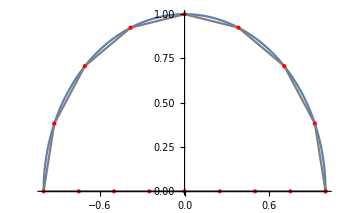

```mathematica
Show[Plot[Sqrt[1-x^2],{x,-1,1}], ListLinePlot[DivisionPointsP,PlotStyle->{PointSize[Large],Gray}],ListPlot[DivisionPointsP,PlotStyle->{PointSize[Large],Red}]]
```

## Implementation of Boundary Element Methods

```mathematica
NumberDivideP= 40;
TotalNumberPointsP=3*NumberDivideP;
```

```mathematica
PointsOnLineP = {};
For[i=0,i≤ NumberDivideP-1,i++,
PointsOnLineP = Insert[PointsOnLineP,-1+(2*i)/NumberDivideP,-1]
];
PointsOnCurveP = {};
For[i=0,i≤ 2*NumberDivideP,i++,
PointsOnCurveP = Insert[PointsOnCurveP,i/(2*NumberDivideP),-1]
];
PointsXP=PointsOnLineP;
For[i = 1,i≤Length[PointsOnCurveP],i++, 
PointsXP = Insert[PointsXP,N[Cos[PointsOnCurveP[[i]]*π]],-1]
];
PointsYP=ConstantArray[0,Length[PointsOnLineP]];
For[i = 1,i≤Length[PointsOnCurveP],i++, 
PointsYP = Insert[PointsYP,N[Sin[PointsOnCurveP[[i]]*π]],-1]
];
SegmentsLenP = {};
For[i=1,i≤ TotalNumberPointsP,i++,
SegmentsLenP=Insert[SegmentsLenP,Norm[N[{PointsXP[[i+1]]-PointsXP[[i]],PointsYP[[i+1]]-PointsYP[[i]]}]],-1]
];
NormalPointsXP ={};
For[i=1,i≤ TotalNumberPointsP,i++,
NormalPointsXP = Insert[NormalPointsXP,(PointsYP[[i+1]]-PointsYP[[i]])/SegmentsLenP[[i]],-1]
];
NormalPointsYP ={};
For[i=1,i≤ TotalNumberPointsP,i++,
NormalPointsYP = Insert[NormalPointsYP,-(PointsXP[[i+1]]-PointsXP[[i]])/SegmentsLenP[[i]],-1]
];
```

```mathematica
FP=Function[{i,k,x,y},
FA=Function[kk,SegmentsLenP[[kk]]^2][k];
FB=Function[{kk,xx,yy},(-NormalPointsYP[[kk]]*(PointsXP[[kk]]-xx)+NormalPointsXP[[kk]]*(PointsYP[[kk]]-yy))*2*SegmentsLenP[[kk]]][k,x,y];
FE=Function[{kk,xx,yy},(PointsXP[[kk]]-xx)^2+(PointsYP[[kk]]-yy)^2][k,x,y];
Decision=4*FA*FE-FB^2;
If[i == 1,
Re[If[Decision==0,SegmentsLenP[[k]]/(2*π)*(Log[SegmentsLenP[[k]]]+(1+FB/(2*FA))*Log[Abs[1+FB/(2*FA)]]-FB/(2*FA)*Log[Abs[FB/(2*FA)]]-1),
SegmentsLenP[[k]]/(4*π)*(2*(Log[SegmentsLenP[[k]]]-1)-FB/(2*FA)*Log[Abs[FE/FA]]+(1+FB/(2*FA))*Log[Abs[1+(FB+FE)/FA]]+Sqrt[Decision]/FA*(ArcTan[(2*FA+FB)/Sqrt[Decision ]]-ArcTan[FB/Sqrt[Decision ]]))
]]
,Re[If[Decision ==0,0,SegmentsLenP[[k]]*((NormalPointsXP[[k]]*(PointsXP[[k]]-x)+NormalPointsYP[[k]]*(PointsYP[[k]]-y))/(π*Sqrt[Decision ]))*(ArcTan[(2*FA+FB)/Sqrt[Decision ]]-ArcTan[FB/Sqrt[Decision ]])
]]
]
];
```

```mathematica
MidPointsXP = PointsOnLineP + 1/(NumberDivideP*2);
For[i=1,i≤ Length[PointsOnCurveP],i++,
MidPointsXP = Insert[MidPointsXP,Cos[(PointsOnCurveP[[i]]+1/(NumberDivideP*4))*π],-1]
];
MidPointsYP = ConstantArray[0,Length[PointsOnLineP]];
For[i=1,i≤ Length[PointsOnCurveP],i++,
MidPointsYP = Insert[MidPointsYP,Sin[(PointsOnCurveP[[i]]+1/(NumberDivideP*4))*π],-1]
];
BoundsP={};
For[i=1,i≤ TotalNumberPointsP,i++,
BoundsP = Insert[BoundsP,N[If[N[MidPointsXP[[i]]^2+MidPointsYP[[i]]^2 ]== 1,1,0]],-1];
];
FactorXP= {};
For[i=1,i≤ TotalNumberPointsP,i++,
FactorXP = Insert[FactorXP,(PointsXP[[i+1]]-PointsXP[[i]])/2+PointsXP[[i]],-1];
]; 
FactorYP= {};
For[i=1,i≤ TotalNumberPointsP,i++,
FactorYP = Insert[FactorYP,(PointsYP[[i+1]]-PointsYP[[i]])/2+PointsYP[[i]],-1];
]; 
aP = {};
For[i=1,i≤ TotalNumberPointsP,i++,
Temp = {};
For[j=1,j≤ TotalNumberPointsP,j++,
Temp = Insert[Temp,N[-FP[1,j,FactorXP[[i]],FactorYP[[i]]]],-1];
];
aP = Insert[aP,Temp,-1];
];
bP = {};
For[i=1,i≤ TotalNumberPointsP,i++,
Temp = {};
For[j=1,j≤ TotalNumberPointsP,j++,
Temp = Insert[Temp,N[BoundsP[[j]]*(-FP[2,j,FactorXP[[i]],FactorYP[[i]]]+Function[{ii,jj},If[ii== jj,1,0]][i,j]/2)],-1];
];
bP = Insert[bP,Sum[Temp[[k]],{k,1,TotalNumberPointsP}],-1];
];
zP=LinearSolve[aP, bP];
BoundsUP = {};
For[i=1,i≤ TotalNumberPointsP,i++,
BoundsUP = Insert[BoundsUP,N[BoundsP[[i]]],-1];
];
BoundsNP = {};
For[i=1,i≤ TotalNumberPointsP,i++,
BoundsNP = Insert[BoundsNP,zP[[i]],-1];
];
```

```mathematica
BEMP=Function[{x,y},Sum[BoundsUP[[i]]*FP[2,i,x,y]-BoundsNP[[i]]*FP[1,i,x,y] ,{i,1,TotalNumberPointsP}]];
```

```mathematica
Plot3D[BEMP[x,y],{x,-1,1},{y,0,Sqrt[1-x^2]}]
```

-Graphics3D-

## Comparison Between Boundary Element Solution and Analytic Solution

```mathematica
PointsPA = {{0.10, 0.20},{0.10,0.30},{0.1,0.40},{0.50,0.20},{0.50,0.30},{0.50,0.40},{0.90,0.20},{0.90,0.30},{0.90,0.40}};
```

```mathematica
ValueP120 = {};
For[i=1,i≤ Length[PointsPA],i++,
ValueP120 = Insert[ValueP120,BEMP[PointsPA[[i,1]],PointsPA[[i,2]]],-1]
]
ValueP120
```

{0.253738,0.374381,0.488345,0.326665,0.469776,0.595548,0.771894,0.895153,0.976404}

```mathematica
ValueP60 ={};
For[i=1,i≤ Length[PointsPA],i++,
ValueP60 = Insert[ValueP60,BEMP[PointsPA[[i,1]],PointsPA[[i,2]]],-1]
]
ValueP60
```

{0.253738,0.374381,0.488345,0.326665,0.469776,0.595548,0.771894,0.895153,0.976404}

```mathematica
PointsPAPolar  = {};
For[i = 1,i≤ Length[PointsPA],i++,
PointsPAPolar = Insert[PointsPAPolar,CoordinateTransform["Cartesian" -> "Polar",PointsPA[[i]] ],-1]
]
PointsPAPolar
```

{{0.223607,1.10715},{0.316228,1.24905},{0.412311,1.32582},{0.538516,0.380506},{0.583095,0.54042},{0.640312,0.674741},{0.921954,0.218669},{0.948683,0.321751},{0.984886,0.418224}}

```mathematica
ValueExact = {};
For[i=1,i≤ Length[PointsPAPolar],i++,
ValueExact= Insert[ValueExact,AnalyticSolution[PointsPAPolar[[i,1]],PointsPAPolar[[i,2]]],-1]
]
ValueExact
```

{0.253707,0.374334,0.488284,0.326623,0.469708,0.595458,0.771599,0.894863,0.976138}

```mathematica
PointsPA2 = {{0.1,0.95},{0.1,0.96},{0.1,0.97},{0.1,0.98},{0.1,0.99}}
```

{{0.1,0.95},{0.1,0.96},{0.1,0.97},{0.1,0.98},{0.1,0.99}}

```mathematica
PointsPAPolar2  = {};
For[i = 1,i≤ Length[PointsPA2],i++,
PointsPAPolar2 = Insert[PointsPAPolar2,CoordinateTransform["Cartesian" -> "Polar",PointsPA2[[i]] ],-1]
]
PointsPAPolar2
```

{{0.955249,1.46592},{0.965194,1.467},{0.975141,1.46807},{0.985089,1.46911},{0.995038,1.47013}}

```mathematica
ValueExact2 = {};
For[i=1,i≤ Length[PointsPAPolar2],i++,
ValueExact2= Insert[ValueExact2,AnalyticSolution[PointsPAPolar2[[i,1]],PointsPAPolar2[[i,2]]],-1]
]
ValueExact2
```

{0.970703,0.97733,0.983891,0.990386,0.996817}

```mathematica
ValueP1202={};
For[i=1,i≤ Length[PointsPA2],i++,
ValueP1202 = Insert[ValueP1202,BEMP[PointsPA2[[i,1]],PointsPA2[[i,2]]],-1]
]
ValueP1202
```

{0.970805,0.977433,0.983994,0.990491,0.996929}

```mathematica
(ValueP1202 - ValueExact2 )
```

{0.000102288,0.000102576,0.000103059,0.00010473,0.000112379}

```mathematica
PointsPA3 = {};
For [i = 1,i ≤ 180,i++,
PointsPA3 = Insert[PointsPA3,N[CoordinateTransform["Polar"-> "Cartesian",{1, i/180 π}],10],-1]
]
```

```mathematica
ValueP1203={};
For[i=1,i≤ Length[PointsPA3],i++,
ValueP1203 = Insert[ValueP1203,BEMP[PointsPA3[[i,1]],PointsPA3[[i,2]]],-1]
]
```

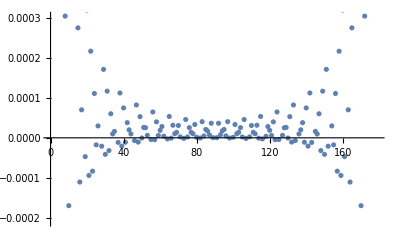

```mathematica
Show[ListPlot[ValueP1203],ListPlot[ConstantArray[1,180]]]
```

## Rough Idea of Dividing Boundary When Applying BEM Using Green Function

```mathematica
DivisionPointsG= {};
For [i = 0,i ≤ 8,i++,
DivisionPointsG = Insert[DivisionPointsG,N[CoordinateTransform["Polar"-> "Cartesian",{1, i/8 π}],10],-1]
]
```

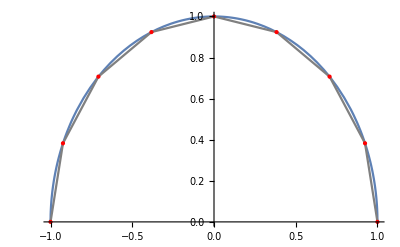

```mathematica
Show[Plot[Sqrt[1-x^2],{x,-1,1}], ListLinePlot[DivisionPointsG,PlotStyle->{PointSize[Large],Gray}],ListPlot[DivisionPointsG,PlotStyle->{PointSize[Large],Red}]]
```

## Implementation of BEM Using Green Function

```mathematica
NumberDivideG= 60;
TotalNumberPointsG=2*NumberDivideG;
```

```mathematica
PointsOnCurveG = {};
For[i=0,i≤ 2*NumberDivideG,i++,
PointsOnCurveG = Insert[PointsOnCurveG,i/(2*NumberDivideG),-1]
];
PointsXG={};
For[i = 1,i≤Length[PointsOnCurveG],i++, 
PointsXG = Insert[PointsXG,N[Cos[PointsOnCurveG[[i]]*π],10],-1]
];
PointsYG={};
For[i = 1,i≤Length[PointsOnCurveG],i++, 
PointsYG = Insert[PointsYG,N[Sin[PointsOnCurveG[[i]]*π],10],-1]
];
SegmentsLenG = {};
For[i=1,i≤ TotalNumberPointsG,i++,
SegmentsLenG=Insert[SegmentsLenG,Norm[N[{PointsXG[[i+1]]-PointsXG[[i]],PointsYG[[i+1]]-PointsYG[[i]]}]],-1]
];
NormalPointsXG ={};
For[i=1,i≤ TotalNumberPointsG,i++,
NormalPointsXG = Insert[NormalPointsXG,(PointsYG[[i+1]]-PointsYG[[i]])/SegmentsLenG[[i]],-1]
];
NormalPointsYG ={};
For[i=1,i≤ TotalNumberPointsG,i++,
NormalPointsYG = Insert[NormalPointsYG,-(PointsXG[[i+1]]-PointsXG[[i]])/SegmentsLenG[[i]],-1]
];
```

```mathematica
FG=Function[{i,k,x,y},
FA=Function[kk,SegmentsLenG[[kk]]^2][k];
FB=Function[{kk,xx,yy},(-NormalPointsYG[[kk]]*(PointsXG[[kk]]-xx)+NormalPointsXG[[kk]]*(PointsYG[[kk]]-yy))*2*SegmentsLenG[[kk]]][k,x,y];
FE=Function[{kk,xx,yy},(PointsXG[[kk]]-xx)^2+(PointsYG[[kk]]-yy)^2][k,x,y];
Decision=4*FA*FE-FB^2;
If[i == 1,
Re[If[Decision==0,SegmentsLenG[[k]]/(2*π)*(Log[SegmentsLenG[[k]]]+(1+FB/(2*FA))*Log[Abs[1+FB/(2*FA)]]-FB/(2*FA)*Log[Abs[FB/(2*FA)]]-1),
SegmentsLenG[[k]]/(4*π)*(2*(Log[SegmentsLenG[[k]]]-1)-FB/(2*FA)*Log[Abs[FE/FA]]+(1+FB/(2*FA))*Log[Abs[1+(FB+FE)/FA]]+Sqrt[Decision]/FA*(ArcTan[(2*FA+FB)/Sqrt[Decision ]]-ArcTan[FB/Sqrt[Decision ]]))
]]
,Re[If[Decision ==0,0,SegmentsLenG[[k]]*((NormalPointsXG[[k]]*(PointsXG[[k]]-x)+NormalPointsYG[[k]]*(PointsYG[[k]]-y))/(π*Sqrt[Decision ]))*(ArcTan[(2*FA+FB)/Sqrt[Decision ]]-ArcTan[FB/Sqrt[Decision ]])
]]
]
];
```

```mathematica
MidPointsXG = {};
For[i=1,i≤ Length[PointsOnCurveG],i++,
MidPointsXG = Insert[MidPointsXG,Cos[(PointsOnCurveG[[i]]+1/(NumberDivideG*4))*π],-1]
];
MidPointsYG = {};
For[i=1,i≤ Length[PointsOnCurveG],i++,
MidPointsYG = Insert[MidPointsYG,Sin[(PointsOnCurveG[[i]]+1/(NumberDivideG*4))*π],-1]
];
BoundsG={};
For[i=1,i≤ TotalNumberPointsG,i++,
BoundsG = Insert[BoundsG,1,-1];
];
FactorXG= {};
For[i=1,i≤ TotalNumberPointsG,i++,
FactorXG = Insert[FactorXG,(PointsXG[[i+1]]-PointsXG[[i]])/2+PointsXG[[i]],-1];
]; 
FactorYG= {};
For[i=1,i≤ TotalNumberPointsG,i++,
FactorYG = Insert[FactorYG,(PointsYG[[i+1]]-PointsYG[[i]])/2+PointsYG[[i]],-1];
]; 
aG = {};
For[i=1,i≤ TotalNumberPointsG,i++,
Temp = {};
For[j=1,j≤ TotalNumberPointsG,j++,
Temp = Insert[Temp,N[-(FG[1,j,FactorXG[[i]],FactorYG[[i]]]-FG[1,j,FactorXG[[i]],-FactorYG[[i]]])],-1];
];
aG = Insert[aG,Temp,-1];
];
bG = {};
For[i=1,i≤ TotalNumberPointsG,i++,
Temp = {};
For[j=1,j≤ TotalNumberPointsG,j++,
Temp = Insert[Temp,N[BoundsG[[j]]*(-FG[2,j,FactorXG[[i]],FactorYG[[i]]]+FG[2,j,FactorXG[[i]],-FactorYG[[i]]]+Function[{ii,jj},If[ii== jj,1,0]][i,j]/2)],-1];
];
bG = Insert[bG,Sum[Temp[[k]],{k,1,TotalNumberPointsG}],-1];
];
zG=LinearSolve[aG, bG];
BoundsUG = {};
For[i=1,i≤ TotalNumberPointsG,i++,
BoundsUG = Insert[BoundsUG,N[BoundsG[[i]]],-1];
];
BoundsNG = {};
For[i=1,i≤ TotalNumberPointsG,i++,
BoundsNG = Insert[BoundsNG,zG[[i]],-1];
];
```

```mathematica
BEMG=Function[{x,y},Sum[BoundsUG[[i]]*(FG[2,i,x,y]-FG[2,i,x,-y])-BoundsNG[[i]]*(FG[1,i,x,y]-FG[1,i,x,-y]) ,{i,1,TotalNumberPointsG}]];
```

```mathematica
Plot3D[BEMG[x,y],{x,-1,1},{y,0,Sqrt[1-x^2]}]
```

-Graphics3D-

## Comparison Between BES Using Green Function and Analytic Solution

```mathematica
PointsGA = {{0.10, 0.20},{0.10,0.30},{0.1,0.40},{0.50,0.20},{0.50,0.30},{0.50,0.40},{0.90,0.20},{0.90,0.30},{0.90,0.40}};
```

```mathematica
ValueG60 = {};
For[i=1,i≤ Length[PointsGA],i++,
ValueG60 = Insert[ValueG60,BEMG[PointsGA[[i,1]],PointsGA[[i,2]]],-1]
]
ValueG60
```

{0.253793,0.374455,0.488432,0.326824,0.469954,0.595719,0.772824,0.895567,0.976611}

```mathematica
ValueG120 = {};
For[i=1,i≤ Length[PointsGA],i++,
ValueG120 = Insert[ValueG120,BEMG[PointsGA[[i,1]],PointsGA[[i,2]]],-1]
]
ValueG120
```

{0.253729,0.374364,0.488321,0.326673,0.469769,0.595523,0.771899,0.895035,0.976256}

```mathematica
PointsGA2 = {{0.10,0.95},{0.10,0.96},{0.10,0.97},{0.10,0.98},{0.10,0.99}}
```

{{0.1,0.95},{0.1,0.96},{0.1,0.97},{0.1,0.98},{0.1,0.99}}

```mathematica
ValueG802={};
For[i=1,i≤ Length[PointsGA2],i++,
ValueG802 = Insert[ValueG802,BEMG[PointsGA2[[i,1]],PointsGA2[[i,2]]],-1]
]
ValueG802
```

{0.970807,0.977434,0.983995,0.990492,0.99693}

```mathematica
ValueG802 - ValueExact2
```

{0.000104368,0.000104222,0.000104274,0.000105507,0.000112669}

```mathematica
ValueG1203={};
For[i=1,i≤ Length[PointsPA3],i++,
ValueG1203 = Insert[ValueG1203,BEMG[PointsPA3[[i,1]],PointsPA3[[i,2]]],-1]
]
```

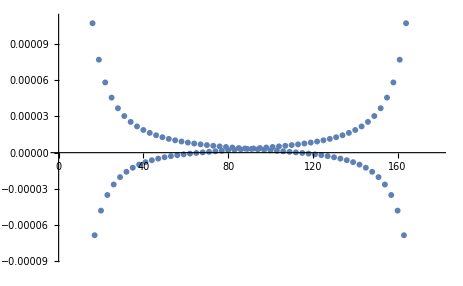

```mathematica
Show[ListPlot[ValueG1203]]
```

## Comparison Between BES and BES Using Green Function

```mathematica
PointsGP = {{0.10,0.85},{0.10,0.88},{0.10,0.90},{0.10,0.93},{0.10,0.95}};
```

```mathematica
ValueG1204={};
For[i = 1,i≤ Length[PointsGP],i++,
ValueG1204 = Insert[ValueG1204,BEMG[PointsGP[[i,1]],PointsGP[[i,2]]],-1];
]
ValueG1204
```

{0.900688,0.922447,0.936596,0.957293,0.970749}

```mathematica
ValueP1204={};
For[i = 1,i≤ Length[PointsGP],i++,
ValueP1204 = Insert[ValueP1204,BEMP[PointsGP[[i,1]],PointsGP[[i,2]]],-1];
]
ValueP1204
```

{0.90074,0.922501,0.93665,0.957348,0.970805}

```mathematica
PointsGPPolar  = {};
For[i = 1,i≤ Length[PointsGP],i++,
PointsGPPolar = Insert[PointsGPPolar,CoordinateTransform["Cartesian" -> "Polar",PointsGP[[i]] ],-1]
]
PointsGPPolar
```

{{0.855862,1.45369},{0.885664,1.45765},{0.905539,1.46014},{0.935361,1.46368},{0.955249,1.46592}}

```mathematica
ValueExactGP={};
For[i = 1,i≤ Length[PointsGPPolar],i++,
ValueExactGP = Insert[ValueExactGP,AnalyticSolution[PointsGPPolar[[i,1]],PointsGPPolar[[i,2]]],-1];
]
ValueExactGP
```

{0.900641,0.922401,0.936549,0.957247,0.970703}

```mathematica
ErrorG120 =ValueG1204 - ValueExactGP
```

{0.0000468309,0.0000467238,0.0000466232,0.0000464328,0.0000462819}

```mathematica
ErrorP120 = ValueP1204  - ValueExactGP
```

{0.0000989915,0.00010014,0.000100826,0.000101743,0.000102288}

## Approximate Real Solution to Mixed Boundary Value Problem

```mathematica
AnalyticSolution2 = NDSolveValue[{-∇_{x,y}^2 u[x,y] == NeumannValue[-1,y==0], DirichletCondition[u[x,y] == 1, x^2 +y^2 == 1]},
  u, {x,y} ∈ Disk[{0,0},1,{0, π}]]
```

InterpolatingFunction[…]

```mathematica
Plot3D[AnalyticSolution2[x,y],{x,y} ∈ Disk[{0,0},1,{0, π}]]
```

-Graphics3D-

## Implementation of BEM to Solve Mixed Boundary Value Problem

```mathematica
NumberDivideM= 40;
TotalNumberPointsM=3*NumberDivideM;
```

```mathematica
PointsOnLineM = {};
For[i=0,i≤ NumberDivideM-1,i++,
PointsOnLineM = Insert[PointsOnLineM,-1+(2*i)/NumberDivideM,-1]
];
PointsOnCurveM = {};
For[i=0,i≤ 2*NumberDivideM,i++,
PointsOnCurveM = Insert[PointsOnCurveM,i/(2*NumberDivideM),-1]
];
PointsXM=PointsOnLineM;
For[i = 1,i≤Length[PointsOnCurveM],i++, 
PointsXM = Insert[PointsXM,N[Cos[PointsOnCurveM[[i]]*π]],-1]
];
PointsYM=ConstantArray[0,Length[PointsOnLineM]];
For[i = 1,i≤Length[PointsOnCurveM],i++, 
PointsYM = Insert[PointsYM,N[Sin[PointsOnCurveM[[i]]*π]],-1]
];
SegmentsLenM = {};
For[i=1,i≤ TotalNumberPointsM,i++,
SegmentsLenM=Insert[SegmentsLenM,Norm[N[{PointsXM[[i+1]]-PointsXM[[i]],PointsYM[[i+1]]-PointsYM[[i]]}]],-1]
];
NormalPointsXM ={};
For[i=1,i≤ TotalNumberPointsM,i++,
NormalPointsXM = Insert[NormalPointsXM,(PointsYM[[i+1]]-PointsYM[[i]])/SegmentsLenM[[i]],-1]
];
NormalPointsYM ={};
For[i=1,i≤ TotalNumberPointsM,i++,
NormalPointsYM = Insert[NormalPointsYM,-(PointsXM[[i+1]]-PointsXM[[i]])/SegmentsLenM[[i]],-1]
];
```

```mathematica
FM=Function[{i,k,x,y},
FA=Function[kk,SegmentsLenM[[kk]]^2][k];
FB=Function[{kk,xx,yy},(-NormalPointsYM[[kk]]*(PointsXM[[kk]]-xx)+NormalPointsXM[[kk]]*(PointsYM[[kk]]-yy))*2*SegmentsLenM[[kk]]][k,x,y];
FE=Function[{kk,xx,yy},(PointsXM[[kk]]-xx)^2+(PointsYM[[kk]]-yy)^2][k,x,y];
Decision=4*FA*FE-FB^2;
If[i == 1,
Re[If[Decision==0,SegmentsLenM[[k]]/(2*π)*(Log[SegmentsLenM[[k]]]+(1+FB/(2*FA))*Log[Abs[1+FB/(2*FA)]]-FB/(2*FA)*Log[Abs[FB/(2*FA)]]-1),
SegmentsLenM[[k]]/(4*π)*(2*(Log[SegmentsLenM[[k]]]-1)-FB/(2*FA)*Log[Abs[FE/FA]]+(1+FB/(2*FA))*Log[Abs[1+(FB+FE)/FA]]+Sqrt[Decision]/FA*(ArcTan[(2*FA+FB)/Sqrt[Decision ]]-ArcTan[FB/Sqrt[Decision ]]))
]]
,Re[If[Decision ==0,0,SegmentsLenM[[k]]*((NormalPointsXM[[k]]*(PointsXM[[k]]-x)+NormalPointsYM[[k]]*(PointsYM[[k]]-y))/(π*Sqrt[Decision ]))*(ArcTan[(2*FA+FB)/Sqrt[Decision ]]-ArcTan[FB/Sqrt[Decision ]])
]]
]
];
```

```mathematica
MidPointsXM = PointsOnLineM + 1/(NumberDivideM*2);
For[i=1,i≤ Length[PointsOnCurveM],i++,
MidPointsXM = Insert[MidPointsXM,Cos[(PointsOnCurveM[[i]]+1/(NumberDivideM*4))*π],-1]
];
MidPointsYM = ConstantArray[0,Length[PointsOnLineM]];
For[i=1,i≤ Length[PointsOnCurveM],i++,
MidPointsYM = Insert[MidPointsYM,Sin[(PointsOnCurveM[[i]]+1/(NumberDivideM*4))*π],-1]
];
BoundsM={};
For[i=1,i≤ NumberDivideM,i++,
BoundsM = Insert[BoundsM,-1,-1];
];
For[i=1,i≤ 2*NumberDivideM,i++,
BoundsM = Insert[BoundsM,1,-1];
];
FactorXM= {};
For[i=1,i≤ TotalNumberPointsM,i++,
FactorXM = Insert[FactorXM,(PointsXM[[i+1]]-PointsXM[[i]])/2+PointsXM[[i]],-1];
]; 
FactorYM= {};
For[i=1,i≤ TotalNumberPointsM,i++,
FactorYM = Insert[FactorYM,(PointsYM[[i+1]]-PointsYM[[i]])/2+PointsYM[[i]],-1];
]; 
aM = {};
For[i=1,i≤ TotalNumberPointsM,i++,
Temp = {};
For[j=1,j≤ NumberDivideM,j++,
Temp = Insert[Temp,N[FM[2,j,FactorXM[[i]],FactorYM[[i]]]-Function[{ii,jj},If[ii== jj,1,0]][i,j]/2],-1];
];
For[j=NumberDivideM+1,j≤NumberDivideM*3,j++,
Temp = Insert[Temp,N[-FM[1,j,FactorXM[[i]],FactorYM[[i]]]],-1];
];
aM = Insert[aM,Temp,-1];
];
bM = {};
For[i=1,i≤ TotalNumberPointsM,i++,
Temp = {};
For[j=1,j≤ NumberDivideM,j++,
Temp = Insert[Temp,N[BoundsM[[j]]*FM[1,j,FactorXM[[i]],FactorYM[[i]]]],-1];
];
For[j=NumberDivideM+1,j≤ NumberDivideM*3,j++,
Temp = Insert[Temp,N[BoundsM[[j]]*(-FM[2,j,FactorXM[[i]],FactorYM[[i]]]+Function[{ii,jj},If[ii== jj,1,0]][i,j]/2)],-1];
];
bM = Insert[bM,Sum[Temp[[k]],{k,1,TotalNumberPointsM}],-1];
];
zM=LinearSolve[aM, bM];
BoundsUM = {};
For[i=1,i≤ NumberDivideM,i++,
BoundsUM = Insert[BoundsUM,zM[[i]],-1];
];
For[i=NumberDivideM+1,i≤ NumberDivideM*3,i++,
BoundsUM = Insert[BoundsUM,N[BoundsM[[i]]],-1];
];
BoundsNM = {};
For[i=1,i≤ NumberDivideM,i++,
BoundsNM = Insert[BoundsNM,N[BoundsM[[i]]],-1];
];
For[i=NumberDivideM+1,i≤ NumberDivideM*3,i++,
BoundsNM = Insert[BoundsNM,zM[[i]],-1];
];
```

```mathematica
BEMM=Function[{x,y},Sum[BoundsUM[[i]]*FM[2,i,x,y]-BoundsNM[[i]]*FM[1,i,x,y] ,{i,1,TotalNumberPointsM}]];
```

```mathematica
Plot3D[BEMM[x,y],{x,-1,1},{y,0,Sqrt[1-x^2]}]
```

-Graphics3D-

## Comparison Between Boundary Element Solution and Approximate Real Solution

```mathematica
PointsMA = {{0.10, 0.20},{0.10,0.30},{0.1,0.40},{0.50,0.20},{0.50,0.30},{0.50,0.40},{0.90,0.20},{0.90,0.30},{0.90,0.40}};
```

```mathematica
ValueM120 = {};
For[i=1,i≤ Length[PointsMA],i++,
ValueM120 = Insert[ValueM120,BEMM[PointsMA[[i,1]],PointsMA[[i,2]]],-1]
]
ValueM120
```

{0.550764,0.629848,0.701225,0.652429,0.724614,0.787831,0.924011,0.959372,0.989907}

```mathematica
ValueM60= {};
For[i=1,i≤ Length[PointsMA],i++,
ValueM60 = Insert[ValueM60,BEMM[PointsMA[[i,1]],PointsMA[[i,2]]],-1]
]
ValueM60
```

{0.551203,0.630278,0.701632,0.653107,0.725203,0.788329,0.924841,0.959895,0.990241}

```mathematica
ValueExactMA = {};
For[i=1,i≤ Length[PointsMA],i++,
ValueExactMA= Insert[ValueExactMA,AnalyticSolution2[PointsMA[[i,1]],PointsMA[[i,2]]],-1]
]
ValueExactMA
```

{0.551841,0.630815,0.702062,0.652624,0.724802,0.788019,0.923646,0.959226,0.989775}

```mathematica
PointsMA2 = {{0.10,0.95},{0.10,0.96},{0.10,0.97},{0.0,0.98},{0,0.99}};
```

```mathematica
ValueM1202= {};
For[i=1,i≤ Length[PointsMA2],i++,
ValueM1202 = Insert[ValueM1202,BEMM[PointsMA2[[i,1]],PointsMA2[[i,2]]],-1]
]
ValueM1202
```

{0.983365,0.987142,0.99088,0.992721,0.996405}

```mathematica
ValueExactMA2 = {};
For[i=1,i≤ Length[PointsMA2],i++,
ValueExactMA2= Insert[ValueExactMA2,AnalyticSolution2[PointsMA2[[i,1]],PointsMA2[[i,2]]],-1]
]
ValueExactMA2
```

{0.983369,0.987134,0.99086,0.992695,0.996367}

```mathematica
ValueM1202 - ValueExactMA2
```

{-3.74495×10^-6,7.97227×10^-6,0.0000207005,0.0000256709,0.0000387372}

```mathematica
PointsMA3 = {};
For [i = 1,i ≤ 180,i++,
PointsMA3 = Insert[PointsMA3,N[CoordinateTransform["Polar"-> "Cartesian",{1, i/180 π}],10],-1]
]
```

```mathematica
ValueM1203={};
For[i=1,i≤ Length[PointsMA3],i++,
ValueM1203 = Insert[ValueM1203,BEMM[PointsMA3[[i,1]],PointsMA3[[i,2]]],-1]
]
```

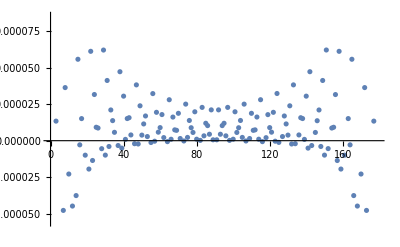

```mathematica
Show[ListPlot[ValueM1203]]
```